```mathematica
ClearAll["Global`*"]
filelist=FileNames["*.TIQ","C:\\Work\\schottky_data_process"];
k=1;
name=ToString[filelist[[k]]]

(*
name=StringTake[filelist[[k]],{-18,-5}]
Export["C:\\Work\\schottky_data_process\\"<>name<>".dat",filelist]*)
```

C:\Work\schottky_data_process\2022.06.172256.tiq

## ** Header report**

```mathematica
(*########### 头文件说明 (XML格式内容) ###############*)
firstLine=Import[filelist[[k]],"List"][[1]]
offset=StringSplit[firstLine,"\""][[2]]//ToExpression;

(*字符串转变*)
head=Import[filelist[[k]],"Byte"][[;;offset]]//FromCharacterCode;
headXML=ImportString[head,"XML"];

center=Cases[headXML,XMLElement[tag="Frequency",_,{data_}]->data,Infinity][[1]]//ToExpression;
bandwidth=Cases[headXML,XMLElement[tag="AcquisitionBandwidth",_,{data_}]->data,Infinity][[1]]//ToExpression;
dataTime=Cases[headXML,XMLElement[tag="DateTime",_,{data_}]->data,Infinity][[1]];
scale=Cases[headXML,XMLElement[tag="Scaling",_,{data_}]->data,Infinity][[1]];
temp=StringSplit[scale,"E"]//ToExpression;
scale=temp[[1]]*10^temp[[2]];

numberSamples=Cases[headXML,XMLElement[tag="NumberSamples",_,{data_}]->data,Infinity][[1]]//ToExpression; (*this entry matches (filesize-offset)/8*)
rfAtt=Cases[headXML,XMLElement[tag="RFAttenuation",_,{data_}]->data,Infinity][[1]]//ToExpression;
fs=Cases[headXML,XMLElement[tag="SamplingFrequency",_,{data_}]->data,Infinity][[1]]//ToExpression;
(*temp=StringSplit[fs,"."]//ToExpression;
fs=N[temp[[1]]+temp[[2]]/10^Length[IntegerDigits[temp[[2]]]],8];*)

rbw=Cases[headXML,XMLElement[tag="NumericParameter",{"pid"->"fmtRBW","name"->"Resolution Bandwidth"},{___,XMLElement["Value",_,{data_}],___}]->data,Infinity][[1]]//ToExpression;
span=Cases[headXML,XMLElement[tag="NumericParameter",{"pid"->"globalrange","name"->"Span"},{___,XMLElement["Value",_,{data_}],___}]->data,Infinity][[1]]//ToExpression;

totalFrames=(FileByteCount[filelist[[k]]]-offset)/numberSamples/8;


Print["------------ Initial Parameters ---------------"]
Print["Timestamp: ",dataTime]
Print["Cnter Frequency: ",center ," Hz",  "    scale factor: ",scale]
Print["span(BW): ",span," Hz"]
Print["number of samples: ",numberSamples//N," "]
Print["Total number of frames:  ", totalFrames//N]
(*Print["Frame length: ",lframes,"  data points= ",lframes/fs//N]*)
(*Print["Total number of frames:  ", totalSamples/fs//N]*)
Print["Sampling rate: ",fs, " Hz"]
Print["Header size:  ",offset," Bytes"]
Print["Total file size:  ",FileByteCount[filelist[[k]]]," Bytes"]
Print["PS: Measurement bandwidth and length are a subset of acquistion bandwidth and length"]
Print["---------------------------------------------"]
```

<DataFile offset="003107916" version="0.3">

------------ Initial Parameters ---------------

Timestamp: 2022-06-17T22:59:53.2028280+08:00

Cnter Frequency: 241982500 Hz    scale factor: 4.16007×10^-11

span(BW): 700000 Hz

number of samples: 4042.

Total number of frames:  7840.

Sampling rate: 1562500 Hz

Header size:  3107916 Bytes

Total file size:  256622156 Bytes

PS: Measurement bandwidth and length are a subset of acquistion bandwidth and length

---------------------------------------------

## ** Data pre-checking **

#### calculated byteCount has a little difference with the information from file.

```mathematica
totalByte=FileByteCount[filelist[[k]]];
Print["####################################"]
Print["Read head size ",offset," Bytes"]
Print["Read File size ",totalByte," Bytes"]

dataHead=ReadByteArray[filelist[[k]]][[;;offset]];
dataSignal=ReadByteArray[filelist[[k]]][[offset+1;;]];
headSize=ByteCount[dataHead];
dataSize=ByteCount[dataSignal];
Print["Cal. head size ",headSize," Bytes"]
Print["Cal. data size ",dataSize," Bytes"]

dataHead=Normal[dataHead];
dataHead//FromCharacterCode;
datasignal=Normal[dataSignal];
datasignal//FromCharacterCode;

dataHead[[-10;;-1]]//FromCharacterCode
datasignal[[1;;10]]//FromCharacterCode
```

####################################

Read head size 1884694 Bytes

Read File size 135173686 Bytes

Cal. head size 1884896 Bytes

Cal. data size 133289192 Bytes

/DataFile>

.00 ëÿ.00°x.00.00°

## ** IQ data translation and FFT (Single frame) **

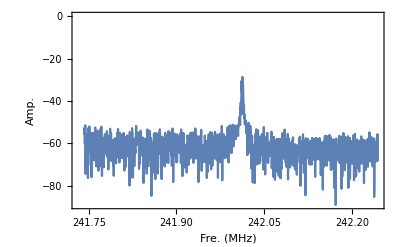

```mathematica
lframes=4042; (*每帧的点数，相当于fs*)
nframes=1; (*读取帧数*)
sframes=5820; (*开始帧数*)

(*提取原始信号数据*)
startP=offset+1+sframes*lframes*8;
endP=offset+1+sframes*lframes*8+nframes*lframes*8;
dataSignal=ReadByteArray[filelist[[k]]][[startP;;endP]];
dataSignal=ImportByteArray[dataSignal,"Integer32"];

(*I/Q信号->傅里叶变换 FFT*)
IQsplit=Length[dataSignal]/2;
dataSignal=ArrayReshape[dataSignal,{IQsplit,2}]; (*Reshape to I and Q data*)
datafre=Fourier[dataSignal[[;;,1]]+I*dataSignal[[;;,2]]];


llfre=Floor[IQsplit/2];(*data range in frequency domain*)
frepoints=Table[i*fs/lframes+center,{i,-llfre,llfre-1}];

signalfre=(Re[datafre]^2+Im[datafre]^2)*scale^2/50;
signalfre=Join[Take[signalfre,-lframes/2],Take[signalfre,lframes/2]];
signalfre=Transpose[{frepoints/10^6,10*Log[10,signalfre*1000]}];

ListLinePlot[signalfre[[1400;;2700]],PlotRange->All,Frame->True,FrameLabel->{"Fre. (MHz)", "Amp."}]
```

```mathematica
deltaT=0.674
```

## ** IQ data translation and fitting for a single frame **

| Estimate | Standard Error | Confidence Interval
a | 25.8389 | 0.455278 | {24.9459,26.7318}
b | 242.005 | 0.00134407 | {242.002,242.007}
c | -63.032 | 0.217134 | {-63.4578,-62.6061}
σ | 0.0701728 | 0.00158175 | {0.0670705,0.0732751}

{{24.9459,26.7318},{242.002,242.007},{-63.4578,-62.6061},{0.0670705,0.0732751}}

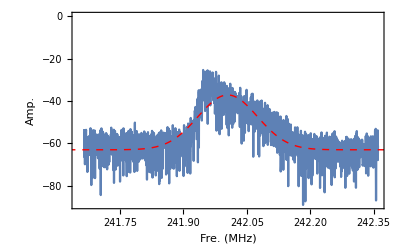

Signal integartion:  4.54498

```mathematica
lframes=4042; (*每帧的点数，相当于fs*)
nframes=1; (*读取帧数*)
sframes=1400; (*开始帧数*)

(*提取原始信号数据*)
startP=offset+1+sframes*lframes*8;
endP=offset+1+sframes*lframes*8+nframes*lframes*8;
dataSignal=ReadByteArray[filelist[[k]]][[startP;;endP]];
dataSignal=ImportByteArray[dataSignal,"Integer32"];

(*I/Q信号->傅里叶变换 FFT*)
IQsplit=Length[dataSignal]/2;
dataSignal=ArrayReshape[dataSignal,{IQsplit,2}]; (*Reshape to I and Q data*)
datafre=Fourier[dataSignal[[;;,1]]+I*dataSignal[[;;,2]]];

frePstart=1200;
frePend=3000;

llfre=Floor[IQsplit/2];(*data range in frequency domain*)
frepoints=Table[i*fs/lframes+center,{i,-llfre,llfre-1}];

signalfre=(Re[datafre]^2+Im[datafre]^2)*scale^2/50;
signalfre=Join[Take[signalfre,-lframes/2],Take[signalfre,lframes/2]];
signalfre=Transpose[{frepoints/10^6,10*Log[10,signalfre*1000]}];
signalfre=signalfre[[frePstart;;frePend]];

figure0 =ListLinePlot[signalfre,PlotRange->All,Frame->True,FrameLabel->{"Fre. (MHz)", "Amp."}];

(*##########################################*)
(*fitting*)
model=a*ⅇ^(-(x-b)^2/(2 *σ^2))+c;
fit=NonlinearModelFit[signalfre,model,{{a,20},{b,242},{c,-65},{σ,0.031}},x];
fit["ParameterConfidenceIntervalTable"]
errors=fit["ParameterErrors"];
confedence=fit["ParameterConfidenceIntervals"]
res=fit["BestFitParameters"];

picfit=Plot[fit//Normal,{x,241,243},PlotStyle->{Red,Thick,Dashed},PlotRange->All];
Show[figure0,picfit]

c0=c/.res;

sum=Integrate[Normal[fit]-c0,{x,241,243}]//N;
Print["Signal integartion:  ",sum]
```

## ** IQ data translation and fitting frame by frame **

```mathematica
lframes=4042; (*每帧的点数，相当于fs*)
nframes=1000; (*读取帧数*)
sframes=5020; (*开始帧数*)

(*提取原始信号数据*)
startP=offset+1+(sframes-1)*lframes*8;
endP=offset+1+(sframes-1)*lframes*8+nframes*lframes*8;
dataSignal=ReadByteArray[filelist[[k]]][[startP;;endP]];
dataSignal=ImportByteArray[dataSignal,"Integer32"];

(*All I/Q信号*)
IQsplit=Length[dataSignal]/2;
dataSignal=ArrayReshape[dataSignal,{IQsplit,2}]; (*Reshape to I and Q data*)
dataSignal=dataSignal[[;;,1]]+I*dataSignal[[;;,2]];

finalRe={{"nframe","time","center ferquency","sigma","integral","background(dBm)"}};

llfre=Floor[IQsplit/nframes/2];(*data range in frequency domain*)
frepoints=Table[i*fs/lframes+center,{i,-llfre,llfre-1}];

frePstart=1200;
frePend=3000;

For[i=1,i≤nframes,i++,
tempdata=dataSignal[[(i-1)*lframes+1;;i*lframes]];
tempfredata=Fourier[tempdata];
signalfre=(Re[tempfredata]^2+Im[tempfredata]^2)*scale^2/50;
signalfre=Join[Take[signalfre,-lframes/2],Take[signalfre,lframes/2]];
signalfre=Transpose[{frepoints/10^6,10*Log[10,signalfre*1000]}];
signalfre=signalfre[[frePstart;;frePend]];

(*##########################################*)
(*fitting*)
model=a*ⅇ^(-(x-b)^2/(2 *σ^2))+c;
fit=NonlinearModelFit[signalfre,model,{{a,20},{b,242},{c,-65},{σ,0.05}},x];
fit["ParameterConfidenceIntervalTable"];
res=fit["BestFitParameters"];
a0=a/.res;
b0=b/.res;
c0=c/.res;
σ0=σ/.res;
sum=NIntegrate[Normal[fit]-c0,{x,241,243}]//N;

finalRe=Append[finalRe,{sframes+i,(sframes+i)*0.0674,b0,σ0,sum,c0}]
];
```

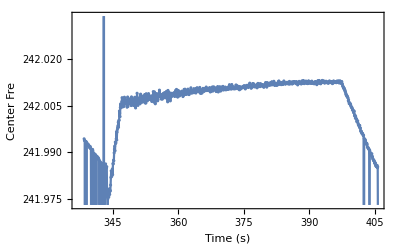

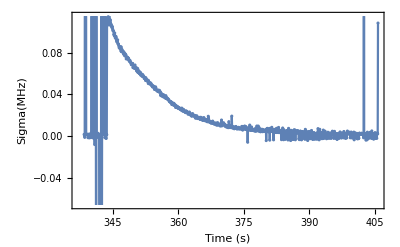

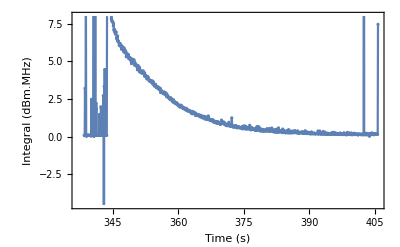

```mathematica
figure1=ListPlot[finalRe[[2;;,{2,3}]],Frame->True,FrameLabel->{"Time (s)","Center Fre"},Joined->True,Mesh->All]
figure1=ListPlot[finalRe[[2;;,{2,4}]],Frame->True,FrameLabel->{"Time (s)","Sigma(MHz)"},Joined->True,Mesh->All]
figure1=ListPlot[finalRe[[2;;,{2,5}]],Frame->True,FrameLabel->{"Time (s)","Integral (dBm.MHz)"},Joined->True,Mesh->All]
```